## Абсолютная скорость шарика

```mathematica
Vx = x'[t] - ϕ'[t] OK ;
Vy = ϕ'[t] (AK - x[t]);
```

```mathematica
V = Sqrt[Vx^2 + Vy^2]
```

√((AK-x[t])^2 ϕ'[t]^2+(x'[t]-OK ϕ'[t])^2)

```mathematica
V^2
```

(AK-x[t])^2 ϕ'[t]^2+(x'[t]-OK ϕ'[t])^2

-Graphics-

## Момент инерции пластины относительно точки вращения

```mathematica
Subscript[J, 0] =  1/18 Subscript[m, 1](3(a)^2 + h^2) + (1/3 h)^2 Subscript[m, 1];
```

## Кинетическая энергия

m1 - пластина, m2 - шарик

```mathematica
T = 1/2 Subscript[J, 0] ϕ'[t]^2+ 1/2 Subscript[m, 2] V^2
```

1/2 ((h^2 m_1)/9+1/18 (3 a^2+h^2) m_1) ϕ'[t]^2+1/2 m_2 ((AK-x[t])^2 ϕ'[t]^2+(x'[t]-OK ϕ'[t])^2)

## Потенциальная энергия

```mathematica
Π =  Subscript[c, 2]/2 (x[t]-Subscript[x, 0])^2 - Subscript[m, 1] g ( 1/3 h Cos[ϕ[t]]) - Subscript[m, 2] g ( OMcos3);
```

-Graphics-

## Геометрия

Координаты шарика

```mathematica
x2 = OA Cos[ϕ[t]]- x[t] Cos[ϕ[t] + α];
y2=y[t] + OA Sin[ϕ[t]] - x[t] Sin[ϕ[t]+ α];
```

```mathematica
OM = Sqrt[x2^2+y2^2];
```

Углы и стороны пластины

```mathematica
OK = h Cos[α];
```

```mathematica
α = ArcTan[h/(a/2)];
```

```mathematica
OA = a/2;
```

```mathematica
AK = a/2 Cos[α];
```

Тройной угол

```mathematica
OMcos3 = OK Cos[ϕ[t]+α] - (AK - x[t]) Sin[ϕ[t]+α];
```

## Уравнения Лагранжа

```mathematica
eq1 = Collect[D[D[T,ϕ'[t]],t] - D[T,ϕ[t]] == -D[Π,ϕ[t]],{ϕ''[t],x''[t]}]
```

-2 m_2 (a/(2 √(1+(4 h^2)/a^2))-x[t]) x'[t] ϕ'[t]-(h m_2 x''[t])/(√(1+(4 h^2)/a^2))+((h^2 m_1)/9+1/18 (3 a^2+h^2) m_1+(h^2 m_2)/(1+(4 h^2)/a^2)+m_2 (a/(2 √(1+(4 h^2)/a^2))-x[t])^2) ϕ''[t]==-1/3 g h Sin[ϕ[t]] m_1+g m_2 (-(h Sin[ArcTan[(2 h)/a]+ϕ[t]])/(√(1+(4 h^2)/a^2))-Cos[ArcTan[(2 h)/a]+ϕ[t]] (a/(2 √(1+(4 h^2)/a^2))-x[t]))

```mathematica
-2 Subscript[m, 2] (AK-x[t]) x'[t] ϕ'[t]-OK Subscript[m, 2] x''[t]+(Subscript[J, 0]+OK^2 Subscript[m, 2]+Subscript[m, 2] (AK-x[t])^2) ϕ''[t]==-1/3 g h Sin[ϕ[t]] Subscript[m, 1]+g Subscript[m, 2] (-OK Sin[α+ϕ[t]]-Cos[α+ϕ[t]] (AK-x[t]))
```

-2 m_2 (a/(2 √(1+(4 h^2)/a^2))-x[t]) x'[t] ϕ'[t]-(h m_2 x''[t])/(√(1+(4 h^2)/a^2))+((h^2 m_1)/9+1/18 (3 a^2+h^2) m_1+(h^2 m_2)/(1+(4 h^2)/a^2)+m_2 (a/(2 √(1+(4 h^2)/a^2))-x[t])^2) ϕ''[t]==-1/3 g h Sin[ϕ[t]] m_1+g m_2 (-(h Sin[ArcTan[(2 h)/a]+ϕ[t]])/(√(1+(4 h^2)/a^2))-Cos[ArcTan[(2 h)/a]+ϕ[t]] (a/(2 √(1+(4 h^2)/a^2))-x[t]))

```mathematica
eq2 = Collect[D[D[T,x'[t]],t] - D[T,x[t]]==-D[Π,x[t]],{ϕ''[t],x''[t]}]
```

m_2 (a/(2 √(1+(4 h^2)/a^2))-x[t]) ϕ'[t]^2+m_2 x''[t]-(h m_2 ϕ''[t])/(√(1+(4 h^2)/a^2))==g Sin[ArcTan[(2 h)/a]+ϕ[t]] m_2-c_2 (-x_0+x[t])

## Параметры

```mathematica
params = {a->6,h->4,Subscript[m, 1] ->5,Subscript[m, 2]->1, g->9.81,Subscript[c, 1]->50,Subscript[x, 0]->3,Subscript[c, 2]->30,Subscript[y, 0]->1};
```

```mathematica
time =5;
```

## Интегрирование

```mathematica
SOLVE = NDSolve[{eq1,eq2,x[0]==2,x'[0]==0,ϕ[0]== Pi/6,ϕ'[0]==0}/.params,{x[t],x'[t],ϕ[t],ϕ'[t],y[t],y'[t]},{t,0,time}]//Flatten
```

{x[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t],ϕ'[t]→InterpolatingFunction[…][t],y[t]→y[t],y'[t]→y'[t]}

```mathematica
SetOptions[Plot,PlotTheme->{"Presentation", "FrameGrid"},ImageSize->Large];
```

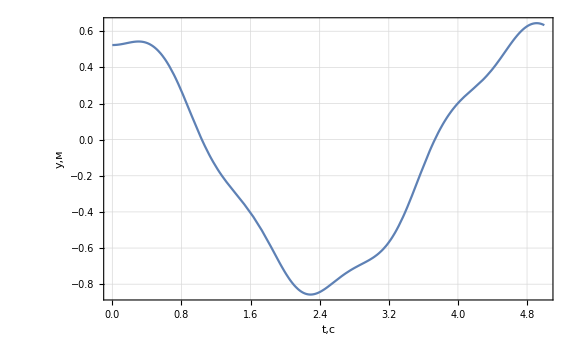

```mathematica
Plot[ϕ[t]/.SOLVE,{t,0,time},Axes->True,FrameLabel->{"t,c","y,м"}]
```

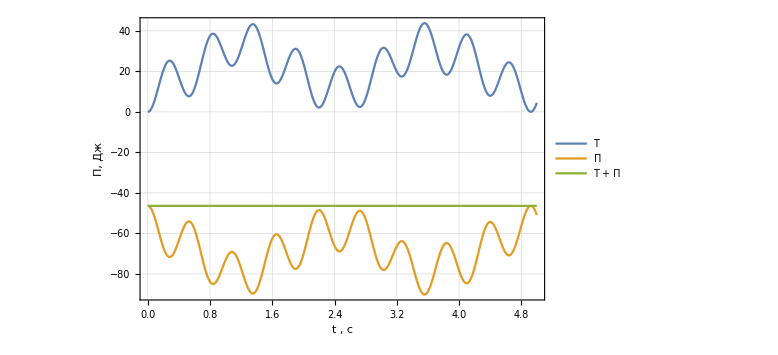

```mathematica
Plot[{T,Π,T+Π}/.SOLVE/.params//Evaluate,{t,0,time},FrameLabel->{"t , c","Π, Дж"},PlotStyle->"Monochrome",PlotStyle->All,PlotLegends->{"T","Π", "T + Π"}]
```

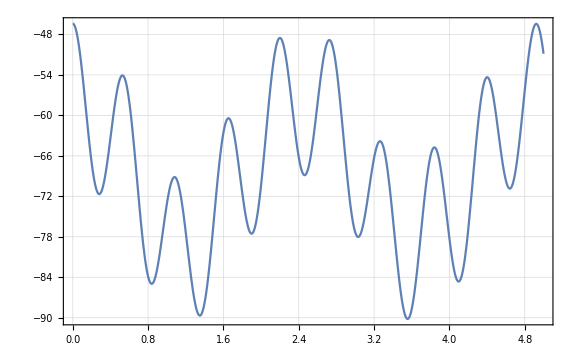

```mathematica
Plot[Π/.SOLVE/.params,{t,0,time}]
```

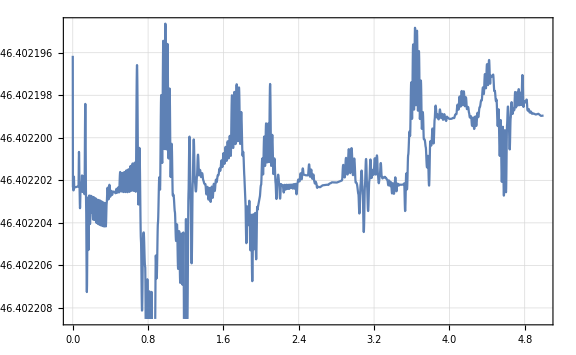

```mathematica
Plot[T+Π/.SOLVE/.params,{t,0,time}]
```